# Coulomb Integral Tables for Diatomic Molecules in Prolate-Spheroidal Coordinates (m==1)

```mathematica
SetDirectory[NotebookDirectory[]];
<<../fermifab.m;
<<diatomic_base.m;
```

## Calculate basic radial integrals √(k_1!/(k_1+m)!k_2!/(k_2+m)!)∫_0^∞ L_k_2^m(x_2)ⅇ^(-x_2/2)arcoth(1+x_2/z)∫_0^x_2 L_k_1^m(x_1)ⅇ^(-x_1/2)ⅆ x_1ⅆ x_2

```mathematica
(* m==1 *)
```

```mathematica
radialIntBaseM1=Parallelize[Outer[RadialLaguerreIntegral[z,1,#1,#2]&,Range[0,37],Range[0,37]]];
```

```mathematica
(* check *)
√(2!/(2+1)! 3!/(3+1)!)NIntegrate[LaguerreL[3,1,x]Exp[-x/2]ArcCoth[1+x/z]Integrate[LaguerreL[2,1,x1]Exp[-x1/2],{x1,0,x}]/.z->3,{x,0,∞}]-N[radialIntBaseM1⟦2+1,3+1⟧/.z->3]
```

2.82135×10^-14

```mathematica
Put[Definition[radialIntBaseM1],"diatomic_coulomb_m1_base.m"];
```

## Hylleraas expansion of 1/(√(2z+x))H_k^m(x)

```mathematica
(* m==1 *)
sqrtExpand=Parallelize[Table[Print["(",k1,",",k2,")"];If[k1≤k2,SqrtHylleraasExpansion[1,k1,k2],SqrtHylleraasExpansion[1,k2,k1]],{k1,0,40},{k2,0,40}]];
```

```mathematica
(* check *)
FullSimplify[sqrtExpand⟦4+1,5+1⟧-Integrate[1/(√(2z+x))HylleraasH[4,1,x]HylleraasH[5,1,x],{x,0,∞},Assumptions->z>0]]
```

0

```mathematica
Put[Definition[sqrtExpand],"diatomic_coulomb_m1_sqrt.m"];
```

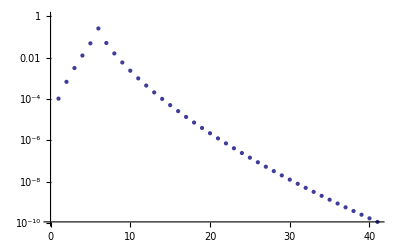

```mathematica
(* convergence plot *)
ListLogPlot[N[Simplify[sqrtExpand⟦5+1,All⟧/.z->3],25]]
```

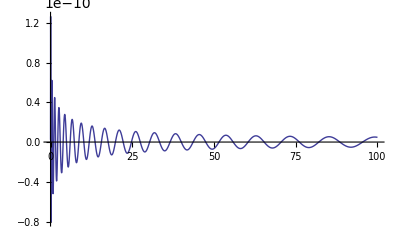

```mathematica
(* check *)
N[Simplify[sqrtExpand⟦5+1,All⟧/.z->3],25];
Plot[(1/(√(2z+x))HylleraasH[5,1,x]/.z->3)-HylleraasExpansion[%,1,x],{x,0,100},PlotRange->All]
```

## Calculate modified radial integrals √(k_1!/(k_1+m)!k_2!/(k_2+m)!)((τ-m)!)/((τ+m)!)∫_0^∞ L_k_2^m(x_2)(x_2^(m/2)(2z+x))^(m/2)Q_τ^m(1+x_2/z)ⅇ^(-x_2/2)∫_0^x_2 L_k_1^m(x_1)x_1^(m/2)√(2z+x)P_τ^m(1+x_1/z)ⅇ^(-x_1/2)ⅆ x_1ⅆ x_2

```mathematica
(* Multiply x^(m/2)LegendreP3[τ,m,1+x/z] by √(2z+x) and x^(m/2)LegendreQ3[τ,m,1+x/z] by (2z+x)^(m/2) to obtain polynomials *)
```

```mathematica
LegendreCoeffMult[τ_,m_,table_]:=Module[{cP=Transpose[LegendrePCoeffsOdd[z,τ,m,Length[table]]],cQ0=Transpose[LegendreQCoeffsOdd0[z,τ,m,Length[table]]],cQ1=Transpose[LegendreQCoeffsOdd1[z,τ,m,Length[table]]],eitab=2NestedLaguerreNormExpIntTable[m,Length[table]]},Parallelize[Table[Simplify[(τ-m)!/(τ+m)!cP⟦i⟧.(table.cQ1⟦j⟧+eitab.cQ0⟦j⟧),Assumptions->z>0,TimeConstraint->∞],{i,Length[cP]},{j,Length[cQ1]}]]]
```

```mathematica
τmax=9;
mval=1;
```

```mathematica
radialModIntM1Tau=Function[τ,Print["τ==",τ];LegendreCoeffMult[τ,mval,radialIntBaseM1]]/@Range[mval,τmax];
```

τ==1

τ==2

τ==3

τ==4

τ==5

τ==6

τ==7

τ==8

τ==9

```mathematica
(* check *)
τval=3;
Integrate[HylleraasH[2,mval,x1] √(2z+x1)LegendreP3[τval,mval,1+x1/z],{x1,0,x},Assumptions->{z>0,x>0}];
(τval-mval)!/(τval+mval)!NIntegrate[HylleraasH[3,mval,x] √(2z+x)LegendreQ3[τval,mval,1+x/z]%/.z->3,{x,0,∞},PrecisionGoal->15,WorkingPrecision->30,MaxRecursion->18]
%-N[radialModIntM1Tau⟦τval-mval+1,2+1,3+1⟧/.z->3,25]
```

0.893332698666816448103366474678

0.

```mathematica
(* check *)
τval=4;
Integrate[HylleraasH[2,mval,x1] √(2z+x1)LegendreP3[τval,mval,1+x1/z],{x1,0,x},Assumptions->{z>0,x>0}];
(τval-mval)!/(τval+mval)!NIntegrate[HylleraasH[3,mval,x] √(2z+x)LegendreQ3[τval,mval,1+x/z]%/.z->3,{x,0,∞},PrecisionGoal->15,WorkingPrecision->30,MaxRecursion->18]
%-N[radialModIntM1Tau⟦τval-mval+1,2+1,3+1⟧/.z->3,25]
```

0.549609955969320487407551680203

-1.×10^-24

```mathematica
Put[Definition[radialModIntM1Tau],"diatomic_coulomb_m1_modint.m"];
```

## Approximate general radial integrals √(k_1!/(k_1+m)!k_2!/(k_2+m)!)((τ-m)!)/((τ+m)!)∫_0^∞ x_2^(m/2)L_k_2^m(x_2)ⅇ^(-x_2/2)Q_τ^m(1+x_2/z)∫_0^x_2 x_1^(m/2)L_k_1^m(x_1)ⅇ^(-x_1/2)P_τ^m(1+x_1/z)ⅆ x_1ⅆ x_2 and perform numeric series expansion in z

```mathematica
(* check *)
Integrate[HylleraasH[2,1,x1]LegendreP3[4,1,1+x1/z],{x1,0,x},Assumptions->{z>0,x>0}];
(4-mval)!/(4+mval)!NIntegrate[HylleraasH[3,1,x]LegendreQ3[4,1,1+x/z]%/.z->3,{x,0,∞},PrecisionGoal->15,WorkingPrecision->30,MaxRecursion->18]
%-N[Simplify[(sqrtExpand⟦2+1,1;;33⟧/.z->3).(radialModIntM1Tau⟦4⟧/.z->3).(sqrtExpand⟦3+1,1;;33⟧/.z->3)],30]
```

0.0297158975881148047501327987988

4.2584491245908021×10^-14

```mathematica
(* Series expansion of a product of 3 functions *)
Total[(Derivative[#1][f][z0])/(#1!)(Derivative[#2][g][z0])/(#2!)(Derivative[#3][h][z0])/(#3!)&@@#&/@GenerateConfig[3,4]];
FullSimplify[%-SeriesCoefficient[f[z]g[z]h[z],{z,z0,4}]]
```

0

```mathematica
ThreeProdSeries[n_,ri_,se_]:=Total[Transpose[se⟦#1⟧].ri⟦#2⟧.se⟦#3⟧&@@#&/@(GenerateConfig[3,n]+1)]
```

```mathematica
MatrixZSeries[expr_,z0_,n_]:=Transpose[Parallelize[Outer[Block[{$MaxExtraPrecision=100},N[Series[#,{z,z0,n}]⟦3⟧,30]]&,expr,2]],{2,3,1}]
```

```mathematica
RadialLaguerreIntZSeries[m_,ri_,se_,z0_,nmax_]:=Module[{riZ,seZ=MatrixZSeries[se,z0,nmax]},Table[Print["τ==",τ];riZ=MatrixZSeries[ri⟦τ-m+1⟧,z0,nmax];Table[N[ThreeProdSeries[n,riZ,seZ⟦All,1;;Length[First[riZ]],1;;Length[First[riZ]]⟧],MachinePrecision],{n,0,nmax}],{τ,m,Length[ri]+m-1}]]
```

```mathematica
(* maximum order of series expansion *)
maxorder=8;
```

```mathematica
For[z0=3,z0≤21,z0+=1/2,
Print["z0==",If[IntegerQ[z0],z0,N[z0]]];
Subscript[radialIntM1TauZ, z0]=RadialLaguerreIntZSeries[mval,radialModIntM1Tau,sqrtExpand,z0,maxorder];
Subscript[radialIntM1TauZ, z0]=Table[PadRight[If[mval≤τ,Subscript[radialIntM1TauZ, z0]⟦τ-mval+1⟧,{{{0}}}],Prepend[Dimensions[Subscript[radialIntM1TauZ, z0]⟦1,1⟧],maxorder+1]],{τ,0,τmax}];
Put[Subscript[radialIntM1TauZ, z0],"diatomic_coulomb_m1_z"<>ToString[If[IntegerQ[z0],z0,N[z0]]]<>".m"];]
```

```mathematica
radialIntM1TauZSeries=Function[z0,{z0,Subscript[radialIntM1TauZ, z0]}]/@Range[3,21,1/2];
(*radialIntM1TauZSeries=Function[z0,{z0,Subscript[radialIntM1TauZ, z0]}]/@({3}∪Range[6,21,1/2]);*)
```

### Save to disk

```mathematica
Put[Definition[radialIntM1TauZSeries],"diatomic_coulomb_m1_zseries.m"];
```

### Compare with numerical integration

```mathematica
RadialIntTest[k1_,k2_,τ_,m_,z_,z0_,inttable_]:=Module[{intInner=Integrate[HylleraasH[k1,m,x1]LegendreP3[τ,m,1+x1/zs],{x1,0,x},Assumptions->{zs>0,x>0}]},
Abs[(τ-m)!/(τ+m)!NIntegrate[HylleraasH[k2,m,x]LegendreQ3[τ,m,1+x/zs]intInner/.zs->z,{x,0,∞},PrecisionGoal->MachinePrecision,WorkingPrecision->30,MaxRecursion->18]-((z-z0)^Range[0,Length[inttable⟦1⟧]-1]).inttable⟦τ+1,All,k1+1,k2+1⟧]]
```

```mathematica
err=(Print["z_0: ",N[First[#]]];RadialIntTest[2,3,2,mval,First[#]+1/10,First[#],Last[#]])&/@radialIntM1TauZSeries
```

z_0: 3.

z_0: 7.

z_0: 7.5

z_0: 8.

z_0: 8.5

z_0: 9.

z_0: 9.5

z_0: 10.

z_0: 10.5

z_0: 11.

z_0: 11.5

z_0: 12.

z_0: 12.5

z_0: 13.

z_0: 13.5

z_0: 14.

z_0: 14.5

z_0: 15.

z_0: 15.5

z_0: 16.

z_0: 16.5

z_0: 17.

z_0: 17.5

z_0: 18.

z_0: 18.5

z_0: 19.

z_0: 19.5

z_0: 20.

z_0: 20.5

z_0: 21.

{1.09551×10^-13,5.55112×10^-17,2.77556×10^-17,2.77556×10^-17,0.,2.77556×10^-17,0.,5.55112×10^-17,5.55112×10^-17,0.,5.55112×10^-17,5.55112×10^-17,0.,0.,5.55112×10^-17,5.55112×10^-17,0.,5.55112×10^-17,5.55112×10^-17,0.,0.,1.11022×10^-16,0.,0.,5.55112×10^-17,5.55112×10^-17,0.,5.55112×10^-17,5.55112×10^-17,0.}